```mathematica
Plot3D[x1+x2,{x1,0,4},{x2,0,4},AxesLabel->Automatic,BoxRatios->{1, 1, 1},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
```

-Graphics3D-

```mathematica
Show[%11,ImageSize->Large]
```

-Graphics3D-

```mathematica
Export["D:\\Category\\#TeX\\Template\\article_notes\\perfect.pdf",Plot3D[x1+x2,{x1,0,4},{x2,0,4},AxesLabel->Automatic,BoxRatios->{1, 1, 1},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]],ImageResolution->1500]
```

D:\Category\#TeX\Template\article_notes\perfect.pdf

```mathematica
Export["D:\\Category\\#TeX\\Template\\article_notes\\.eps",%11,"EPS"]
```

D:\Category\#TeX\Template\article_notes\.eps

```mathematica
Plot3D[x+y,{x,0,5},{y,0,5},PlotPoints->32,MaxRecursion->2]
```

-Graphics3D-

```mathematica
Show[%1,ViewPoint->{∞,0,0}]
```

-Graphics3D-

```mathematica
Plot3D[x/Exp[x^2+y^2],{x,-2,2},{y,-2,2},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
```

-Graphics3D-

```mathematica
𝒟=MeshRegion[{{0,0},{5,-2},{3,0},{5,2}},Polygon[{1,2,3,4}]];
```

```mathematica
Plot3D[x^2+y^2,{x,y}∈MeshRegion[{{0,0},{0,2},{3,0}},Polygon[{1,2,3}]]]
```

-Graphics3D-

```mathematica
Plot3D[x1+x2,{x1,x2}∈MeshRegion[{{0,0},{0,3},{2,0}},Polygon[{1,2,3}]],AxesLabel->Automatic,BoxRatios->{2,3,1.5},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
```

-Graphics3D-

-Graphics3D-

```mathematica
Export["D:\\Category\\#TeX\\Template\\article_notes\\perfectC.pdf",%41,ImageResolution->1600]
```

D:\Category\#TeX\Template\article_notes\perfectC.pdf

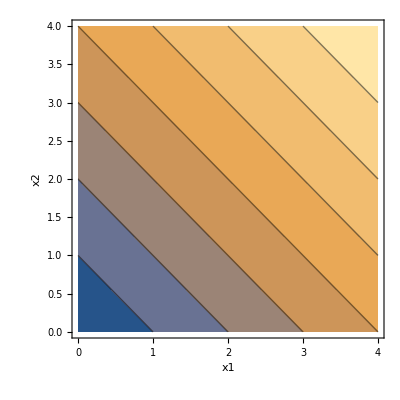

```mathematica
ContourPlot[x1+x2,{x1,0,4},{x2,0,4},AxesLabel->Automatic]
```

```mathematica
Export["D:\\Category\\#TeX\\Template\\article_notes\\indifference.pdf",%32,ImageResolution->1600]
```

D:\Category\#TeX\Template\article_notes\indifference.pdf

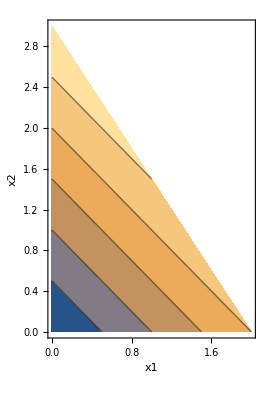

```mathematica
ContourPlot[x1+x2,{x1,x2}∈MeshRegion[{{0,0},{0,3},{2,0}},Polygon[{1,2,3}]],AspectRatio->Automatic, AxesLabel->Automatic]
```

```mathematica
Export["D:\\Category\\#TeX\\Template\\article_notes\\indifferenceC.pdf",%55,ImageResolution->1600]
```

D:\Category\#TeX\Template\article_notes\indifferenceC.pdf

```mathematica
Plot3D[Min[x1,x2],{x1,0,4},{x2,0,4},AxesLabel->Automatic,BoxRatios->{1, 1, 1},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
```

-Graphics3D-

```mathematica
Export["D:\\Category\\#TeX\\Template\\article_notes\\PC.pdf",%57,ImageResolution->1600]
```

D:\Category\#TeX\Template\article_notes\PC.pdf

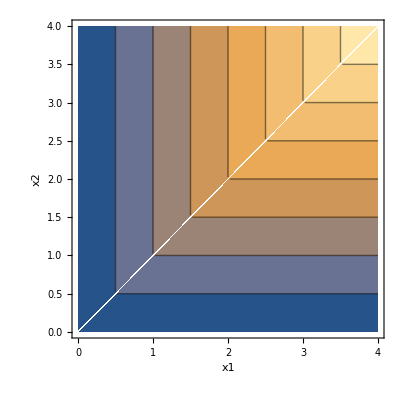

```mathematica
ContourPlot[Min[x1,x2],{x1,0,4},{x2,0,4},AxesLabel->Automatic]
```

```mathematica
Export["D:\\Category\\#TeX\\Template\\article_notes\\PCI.pdf",%59,ImageResolution->1600]
```

D:\Category\#TeX\Template\article_notes\PCI.pdf

```mathematica
Plot3D[(Abs[x1+x2]-Abs[x1-x2])/2,{x1,x2}∈MeshRegion[{{0,0},{0,3},{2,0}},Polygon[{1,2,3}]],AxesLabel->Automatic,BoxRatios->{2,3,1.5},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]]]
```

-Graphics3D-

```mathematica
Plot3D[Min[x1,x2],{x1,0,4},{x2,0,4},RegionFunction->Function[{x1,x2,x3},3*x1+2*x2≤6],AxesLabel->Automatic,BoxRatios->{2,3,1.5},ColorFunction->Function[{x,y,z},Hue[.65 (1-z)]],Exclusions->None]
```

-Graphics3D-

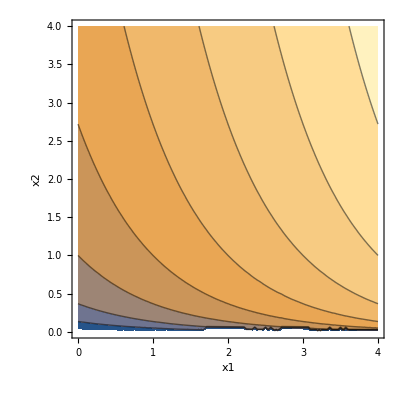

```mathematica
ContourPlot[x1+Log[x2],{x1,0,4},{x2,0,4},AxesLabel->Automatic]
```

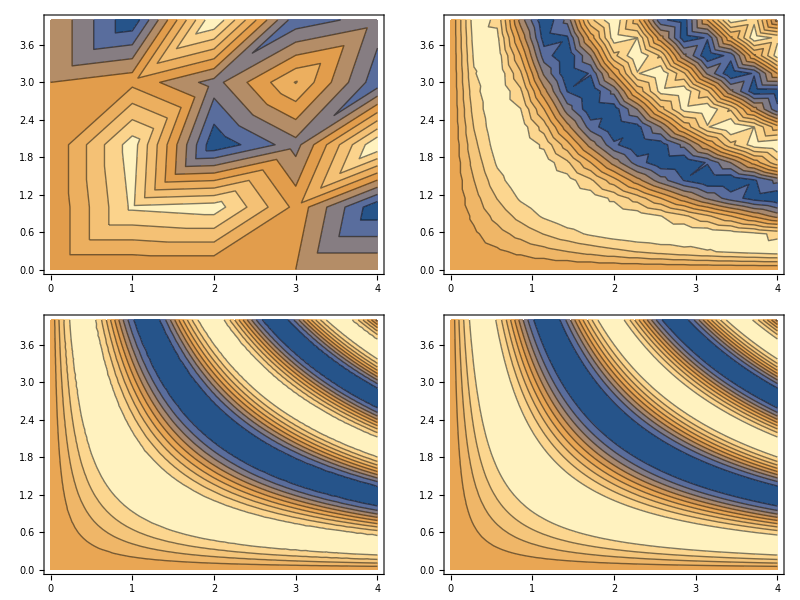

ContourPlot::invmaxrec: MaxRecursion must be a non-negative integer; the recursion value is limited to 15. Using MaxRecursion -> 15.

```mathematica
Grid[Table[ContourPlot[Sin[x y],{x,0,4},{y,0,4},PlotPoints->pp,MaxRecursion->mr],{mr,{0,2}},{pp,{5,15}}]]
```

```mathematica
ContourPlot[Sin[x y],{x,0,4},{y,0,4}]
```

```mathematica
ContourPlot[x1+Log[x2],{x1,0,4},{x2,0,4},AxesLabel->Automatic]
```

-Graphics-

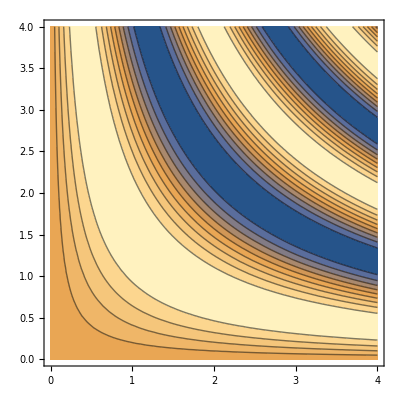

```mathematica
ContourPlot[Sin[x y],{x,0,4},{y,0,4}]
```

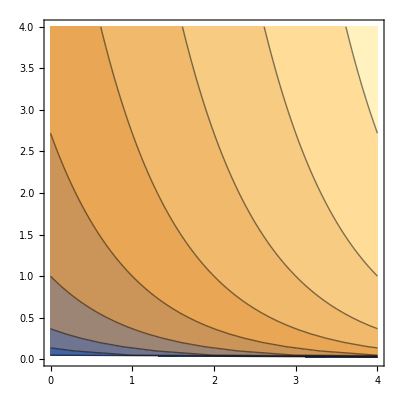

```mathematica
ContourPlot[x1+Log[x2],{x1,0,4},{x2,0,4},Mesh->None,MaxRecursion->0,PlotPoints->80]
```

```mathematica
Export["D:\\CHY\\LaTeX\\Notes\\preference-and-utility\\f2.pdf",%12,ImageResolution->1600]
```

D:\CHY\LaTeX\Notes\preference-and-utility\f2.pdf